# 单圆线解析校准

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## 模型、输入与适用范围

∇.b2Ez−jωμσEz=0; Zint=κ I0(κa)/(2πaσ I1(κa))

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

修改频率与总电流，核对独立电流积分与焦耳积分。

## 推导与结果解释

均匀长圆柱导体的轴对称内场仅保留 Ez(r)，并有 Jz=σEz。由安培与法拉第定律及 exp(+jωt) 得 (1/r)d(r dEz/dr)/dr=jωμσEz；轴心正则解为 C I0(κr)，κ.b2=jωμσ。

用 2π∫Jz r dr=It 确定 C，得到内阻抗 Zint=κ I0(κa)/(2πaσ I1(κa))。独立积分 ∫|J|.b2/σ dA，与 |It|.b2 Re Zint 比较；采用 RMS 相量，无额外 1/2 系数。

κa→0 时 I0→1、I1→κa/2，因此 Rdc=1/(σπa.b2)。模型不含端效应与回流外电感。Q1 的 a=1 mm 保留为解析校准。

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## 可编辑参数

```mathematica
parameters=<|"frequency_Hz"->200000.,"current_RMS_A"->20.|>;parameters
```

<|frequency_Hz -> 200000., current_RMS_A -> 20.|>

## 独立进程执行与结果

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"wolfram-analytic",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_wolfram_analytic_20261014074618_504e7e3b, 
 
>   source_model -> wolfram-analytic, execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

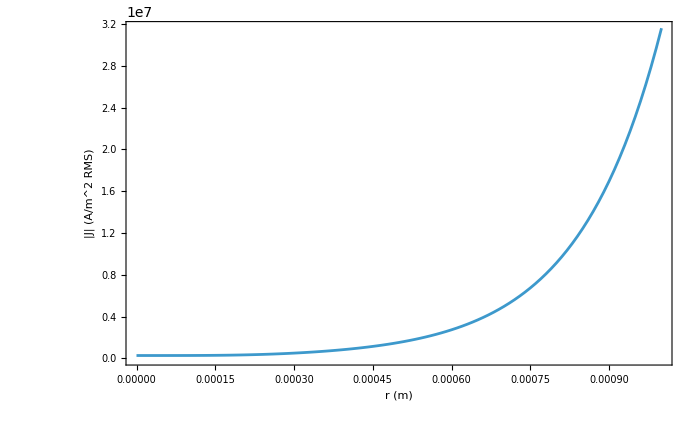

```mathematica
LitzNotebook`DisplayResearch[research]
```

## 验收与接续

核对结果中的 checks、execution_status 和 physical_acceptance_status。完整收敛与结构研究按路线 README 继续。

Sources: BESSEL; references/library.bib and references/sources.json

## 历史证据

data/evidence/v1.0.0-rc.1/; litz-research data fetch analytic